## Read FreeFEM mesh file

```mathematica
(*the path to the mesh file*)
```

```mathematica
fn="~/wwg.msh"
```

~/wwg.msh

```mathematica
stream1=OpenRead[fn]
```

InputStream[…]

```mathematica
{n1,n2,n3}=Read[stream1,{Number,Number,Number}]
```

{293,520,64}

```mathematica
frm=Table[{Real,Real,Number},{n1}];
```

```mathematica
p=Read[stream1,frm];
```

```mathematica
p1=Table[{p[[i,1]],p[[i,2]]},{i,Length[p]}];
```

```mathematica
frm=Table[{Number,Number,Number,Number},{n2}];
```

```mathematica
tr=Read[stream1,frm];
```

```mathematica
tr1=Table[{tr[[i,1]],tr[[i,2]],tr[[i,3]],tr[[i,1]]},{i,Length[tr]}];
```

```mathematica
frm=Table[{Number,Number,Number},{n3}];
```

```mathematica
vt=Read[stream1,frm];
```

```mathematica
lp1=Map[p1[[#]]&,tr1];
```

```mathematica
lp2=Map[Line,lp1];
```

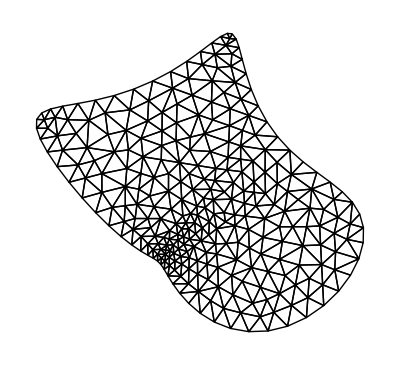

```mathematica
Show[Graphics[lp2]]
```

## Read solution file

```mathematica
(*the path to the values*)
```

```mathematica
fn="~/u.out"
```

~/u.out

```mathematica
stream1=OpenRead[fn]
```

InputStream[…]

```mathematica
n4=Read[stream1,Number]
```

293

```mathematica
frm=Table[Real,{n4}];
```

```mathematica
r=Read[stream1,frm];
```

```mathematica
Close[stream1];
```

```mathematica
Dimensions[r]
```

{293}

## Normalization of value of solution

```mathematica
m1=Min[r];
```

```mathematica
r=r-m1;
```

```mathematica
m1=Max[r];
```

```mathematica
r=r/m1;
```

```mathematica
r2=Table[(r[[tr[[i,1]]]]+r[[tr[[i,2]]]]+r[[tr[[i,3]]]])/3.0,{i,Length[tr]}];
```

## Make colored polygons

```mathematica
p3=Table[{(p1[[tr[[i,1]]]]+p1[[tr[[i,2]]]])*0.5,(p1[[tr[[i,2]]]]+p1[[tr[[i,3]]]])*0.5,(p1[[tr[[i,3]]]]+p1[[tr[[i,1]]]])*0.5},{i,Length[tr]}];
```

```mathematica
plg=Table[{{Hue[r[[tr[[i,1]]]]],Polygon[{p3[[i,1]],p3[[i,1]],p3[[i,3]]}]},{Hue[r2[[i]]],Polygon[{p3[[i,1]],p3[[i,2]],p3[[i,3]]}]},{Hue[r[[tr[[i,2]]]]],Polygon[{p3[[i,2]],p3[[i,2]],p3[[i,1]]}]},{Hue[r[[tr[[i,3]]]]],Polygon[{p3[[i,3]],p3[[i,3]],p3[[i,2]]}]}},{i,Length[tr]}];
```

## Show colored polygons

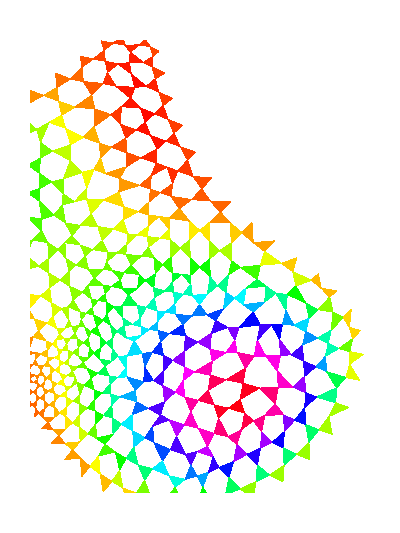

```mathematica
Show[Graphics[plg],PlotRange->{{-.25,1.25},{-1,1}},AspectRatio->2/1.5]
```